## Moretti+ 2003 Log_10(N)-Log_10(S) relation: manipulation, verification, application

Aaron Tran, 2016 August 16.  Trying to refine sky X-ray background model for G309 spectrum fits, and better comprehend unresolved/resolved source flux calculation.

## Relation

Functional form for integral source flux distribution N(>S), from equation (2) of Moretti+ (2003).  Basically, a broken power law smoothly joined at S=S0.
Compare result to Moretti+ (2003) Figure 4, upper panel.

```mathematica
integralSFD[S_,α_,β_,S0_,N0_]:=N0*(2×10^-15)^α/(S^α+S0^(α-β)×S^β);
hardN[S_]:=integralSFD[S,1.57,0.44,4.5 10^-15,5300];
softN[S_]:=integralSFD[S,1.82,0.60,1.48×10^-14,6150];
```

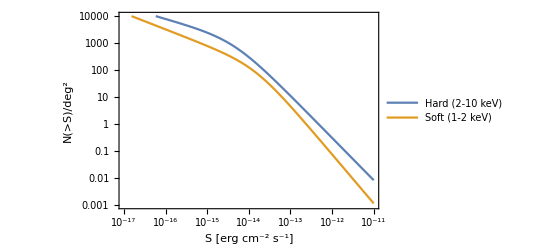

```mathematica
LogLogPlot[{hardN[x],softN[x]},{x,10^-17,10^-11},PlotRange->{{10^-17,10^-11},{10^-3 ,10^4}},
PlotLegends->{"Hard (2-10 keV)","Soft (1-2 keV)"},
FrameLabel->{"S [erg cm^-2 s^-1]","N(>S)/deg^2"},Frame->True]
```

## Manipulation

Check form of dN(>S)/dS against Moretti+ (2003) Figure 4, lower panel.

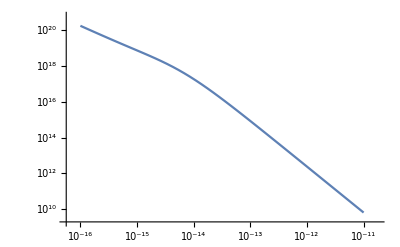

```mathematica
LogLogPlot[-5*D[hardN[s],s]/.{s->x},{x,10^-16,10^-11}]
```

Troubleshooting Mathematica integration (Integrate[...] returns funky results).
If I break the integration steps apart (don’t introduce floating point numbers until the last minute, the results seem best matched to results from NIntegrate[...] rather than Integrate[...].
I am having trouble getting Integrate[...] to work correctly, so I’ll just use NIntegrate[...].

```mathematica
Integrate[-x*D[hardN[s],s]/.{s->x},{x,2.1*10^-16,8*10^-12}]
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,2.1*10^-16,8*10^-12},AccuracyGoal->Infinity,PrecisionGoal->10]
```

0.

1.73483×10^-11

```mathematica
intres=Integrate[-S*D[N0*(2×10^-15)^α/(S^α+S0^(α-β)×S^β),S],S]
```

500000000000000^-α N0 S S0^β (-1/(S^β S0^α+S^α S0^β)+(S^-β S0^-α α)/((-1+β) (-α+β)))-(500000000000000^-α N0 S^(1-β) S0^(-α+β) (α+(-α+β) Hypergeometric2F1[1,(-1+β)/(-α+β),1+(-1+β)/(-α+β),-S^(α-β) S0^(-α+β)]))/((-1+β) (-α+β))

```mathematica
lb=intres/.{α->1.57,β->0.44,S0->4.5*^-15,N0->5300,S->2.1*^-16};
hb=intres/.{α->1.57,β->0.44,S0->4.5*^-15,N0->5300,S->8*^-12};
hb-lb
```

1.73483×10^-11

## Verification

Check integrated flux values against different workers’ results (compare Mathematica’s plain Integrate vs. NIntegrate as well).  First, check the integrated fluxes from Moretti+ (2003).

Moretti+ (2003, Sec. 7.2) obtain integrated 2-10 keV flux of (1.75±0.11)×10^-11 erg cm^-2 sec^-1 deg^-2, from their flux interval 2.1×10^-16 to 7.79×10^-12 erg cm^-2 sec^-1.

```mathematica
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,2.1*10^-16,7.79*10^-12},AccuracyGoal->Infinity,PrecisionGoal->10]
```

1.73444×10^-11

Moretti+ (2003, Sec. 7.1) obtain integrated 0.5-2 keV flux of (6.85±0.3)×10^-12 erg cm^-2 sec^-1 deg^-2 over flux interval 2.44×10^-17 to 10^-11 erg cm^-2 sec^-1.
Note the use of softN[...] rather than hardN[...] above.

```mathematica
NIntegrate[-x*D[softN[s],s]/.{s->x},{x,2.44*10^-17,10^-11},AccuracyGoal->Infinity]
```

6.8571×10^-12

Now check computed values from other papers for sanity.

Bulbul+ (2016, ApJ 818) compute unresolved point source flux in 2-10 keV band: F_CXB=(1.20±0.43)×10^-11=(2.18±0.13)×10^-11-∫(S×dN/dS) dS, so integral should be 0.98×10^-11 erg cm^-2 sec^-1 deg^-2 (for limits: 1.3×10^-14 to 8×10^-12 erg cm^-2 sec^-1).
I get a closer result if I modify the limits from those stated by Bulbul+.  Ask Scott about this...

```mathematica
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,1.3*10^-14,8*10^-12},AccuracyGoal->Infinity]
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,10^-14,10^-8},AccuracyGoal->Infinity]
```

8.39193×10^-12

9.62045×10^-12

Walker+ (2012, MNRAS 422) use the same procedure as Bulbul+ (2016); the integral should be 0.31×10^-11 = 2.18×10^-11 - 1.87×10^-11 erg cm^-2 sec^-1 deg^-2, for 2-10 keV band.
They state lower flux bound of 10^-13 , but don’t explicitly give S_max, so that might be either Moretti’s flux bound 8×10^-12 or just +∞ (or the bright source correction from Moretti Sec. 3).

```mathematica
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,10^-13,8*10^-12},AccuracyGoal->Infinity]
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,10^-13,10^-8},AccuracyGoal->Infinity]
```

2.82854×10^-12

3.08239×10^-12

Henley & Shelton (2013) obtain integrated 0.5-2 keV flux of faint sources 2.97×10^-12 erg cm^-2 sec^-1 deg^-2 for flux range 2.5×10^-17 to 10^-14 erg cm^-2 sec^-1.
Note the use of softN[...] rather than hardN[...] above.

```mathematica
NIntegrate[-x*D[softN[s],s]/.{s->x},{x,2.5*10^-17,10^-14},AccuracyGoal->Infinity]
```

2.97181×10^-12

## Application

The nominal source flux threshold from the ESAS “cheese” task is 10^-14 erg cm^-2 sec^-1 over the 0.4-7.2 keV band. Assuming typical point source photon index Γ=1.4, this translates to flux 9.16×10^-15 erg cm^-2 sec^-1 in the 2-10 keV band.  With absorbing column ~2×10^22 cm^-2, the actual threshold is 1.59×10^-14 in the 0.4-7.2 keV band, or 1.46×10^-14 in the 2-10 keV band.
(computed using XSPEC commands:
    data (...anything...)
    abund wilm
    lmod absmodel ../../../../absmodel/
    xset POW_EMIN 0.4
    xset POW_EMAX 7.2
    mo tbnew_gas*powerlaw
    2
    1.4
    1e-2
    flux 0.4 7.2  # How much was the flux attenuated by absorption
    newpar 4 1.5895e-2  # Rescale normalization so that absorbed flux is 1e-14
    flux 0.4 7.2  # Confirm that absorbed flux is now 1e-14
    newpar 1 0  # Reset absorption
    flux 2 10  # Confirm that unabsorbed flux threshold now is 1.46e-14 (same linear scaling)
)

The flux threshold is still a bit higher than I state because:
1. point source removal is not as effective for sources “within” the remnant, but I neglect this effect.

```mathematica
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,1.46*10^-14,8*10^-12},AccuracyGoal->Infinity]
```

7.97009×10^-12

To extrapolate to higher flux sources in 2-10 keV band, Moretti+ (2003, Sec. 3) use HEAO-1 A2 survey, which yields brightness 4.28×10^-13 erg cm^-2 sec^-1 deg^-2 for all sources with flux > 3.1×10^-11 ergs cm^-2 sec^-1; for the gap from 8×10^-12 to 3.1×10^-11 ergs cm^-2 sec^-1, Moretti+ interpolate their fitted source distribution. The “correct” integrated flux that I removed by excluding point sources is thus:

```mathematica
excludedHardBrightness=4.28*^-13+NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,1.46*10^-14,3.1*10^-11},AccuracyGoal->Infinity]
```

8.53702×10^-12

As expected, this is not too far off from value obtained by extrapolating Moretti’s distribution to high flux:

```mathematica
NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,1.46*10^-14,10^-8},AccuracyGoal->Infinity]
```

8.22394×10^-12

Now use this to rescale our X-ray background.
The Hickox/Markevitch (2006) power law has photon index Γ=1.4, normalization 10.9 photons cm^-2 sec^-1 keV^-1 sr^-1 = 0.00332 photons cm^-2 sec^-1 keV^-1 deg^-2 AT 1 keV.
(units are surprisingly tricky to work out).
The flux from 2-10 keV (and 1-2, 2-8 keV fluxes for validation -- agree with both XSPEC flux command and Hickox/Markevitch):

```mathematica
Γ=1.4;
kev2erg=1.6021766×10^-9;
CXBTotalBrightness=Integrate[(en)*10.9*(180/π)^-2*(en)^-Γ,{en,2,10}]*kev2erg
Integrate[(en)*10.9*(180/π)^-2*(en)^-Γ,{en,1,2}]*kev2erg
Integrate[(en)*10.9*(180/π)^-2*(en)^-Γ,{en,2,8}]*kev2erg
```

2.18585×10^-11

4.57248×10^-12

1.74354×10^-11

Therefore, we should scale down the normalization by a factor:

```mathematica
excludedHardBrightness/CXBTotalBrightness
```

0.390559

## Extra validation

This seems like a high scale-down factor (looked higher before I added absorption correction).  Compare to Revnivtsev+ (2009, Nature, pg. 1142, 2nd column, 2nd full paragraph).  They state that 31% of flux comes from sources brighter than 2×10^-14 erg cm^-2 sec^-1.  Confirm their numbers, with and without Moretti+ (2003, Sec. 3) re-addition of brightest source flux.
Note that they provide 2-10 keV total CXB flux of 2.19×10^-11 erg cm^-2 sec^-1 deg^-2 , which agrees with our calculation (as expected).

```mathematica
Print["Min excluded flux: ",NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,2*10^-14,8*10^-12},AccuracyGoal->Infinity]]
Print["Max excluded flux: ",4.28*^-13+NIntegrate[-x*D[hardN[s],s]/.{s->x},{x,2*10^-14,3.1*10^-11},AccuracyGoal->Infinity]]
```

Min excluded flux: 6.87353×10^-12

Max excluded flux: 7.44046×10^-12

Yes, it works out if brightest sources are not accounted for.  But, even if added, it’s only a 10% effect, which is negligible for their study.

```mathematica
Print["Min excluded fraction: ",6.87*^-12/(2.19*^-11)]
Print["Min excluded fraction: ",7.44*^-12/(2.19*^-11)]
```

Min excluded fraction: 0.313699

Min excluded fraction: 0.339726